A: The current reaction happens before the end time. B: The next reaction happens after the end time. λ is rate (propensity) for the next reaction. Record the current state with probability:

P(A∧¬B)=(∫_0)^T H(A;t)(∫_(T-t))^∞E(λ;s)ⅆsⅆt

For the exponential distribution:

pdf=λ ⅇ^(-λ t)

cdf=1-ⅇ^(-λ t)

```mathematica
Integrate[λ Exp[-λ s],{s,T-t,∞}]
```

λ If[Re[λ]>0,ⅇ^((t-T) λ)/λ,Integrate[ⅇ^(-s λ),{s,-t+T,∞},Assumptions→Re[λ]≤0]]

```mathematica
Integrate[λ Exp[-λ s],{s,0,T-t}]
```

1-ⅇ^((t-T) λ)

Now we simplify the recording probability.

P(A∧¬B)=(∫_0)^T H(A;t)ⅇ^(-λ(T-t))ⅆt

The hypoexponential distribution has mean

μ=(∑_(i=1))^n 1/λ_i

and variance

σ^2=(∑_(i=1))^n 1/λ_i^2

We approximate the hypoexponential distribution with the normal distribution.

```mathematica
Integrate[1/(σ √(2π))Exp[(-(t-μ)^2)/(2 σ^2)]Exp[-λ(T-t)],{t,0,T}]
```

1/2 ⅇ^(1/2 λ (-2 T+2 μ+λ σ^2)) (Erf[(μ+λ σ^2)/(√2 σ)]+Erf[-(-T+μ+λ σ^2)/(√2 σ)])

P(A∧¬B)=1/2 ⅇ^(-λ(T-μ-λ σ^2/2))(erf((μ+λ σ^2)/(√2 σ))+erf((T-μ-λ σ^2)/(√2 σ)))

For the special case λ=0, this is

P(A∧¬B)=1/2(erf(μ/(√2 σ))+erf((T-μ)/(√2 σ)))

```mathematica
Integrate[1/(σ √(2π))Exp[(-(t-μ)^2)/(2 σ^2)],{t,0,T}]
```

1/2 (Erf[(T-μ)/(√2 σ)]+Erf[μ/(√2 σ)])

For large μ/σ, the probability simplifies to

P(A∧¬B)=1/2 ⅇ^(-λ(T-μ-λ σ^2/2))(1+erf((T-μ-λ σ^2)/(√2 σ)))

Consider T=μ.

P(A∧¬B)=1/2 ⅇ^(λ^2 σ^2/2)(1+erf((-λ σ)/(√2)))

```mathematica
1/2*Exp[10000/2]*(1+Erf[-100/√2])//N
```

0.

Take T=10, λ=1, μ=x, σ^2=x.

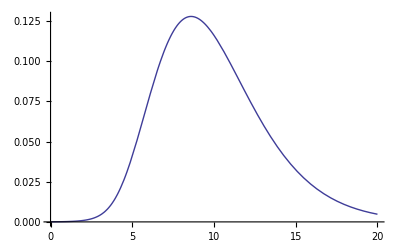

```mathematica
Plot[1/2 Exp[-(10-x-x/2)](1+Erf[(10-x-x)/(√(2x))]),{x,0,20}]
```

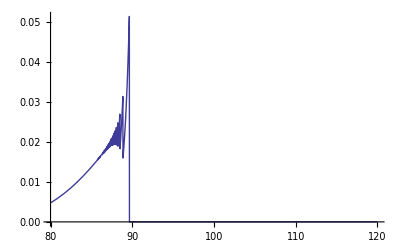

```mathematica
Plot[1/2 Exp[-(100-x-x/2)](1+Erf[(100-x-x)/(√(2x))]),{x,80,120},PlotRange->All]
```

```mathematica
N[1/2 Exp[-(100-x-x/2)](1+Erf[(100-x-x)/(√(2x))])/.x->100,20]
```

0.03950669410138600294

```mathematica
Plot[1/2 Exp[-(100-x-x/2)],{x,80,120},PlotRange->All]
```

-Graphics-

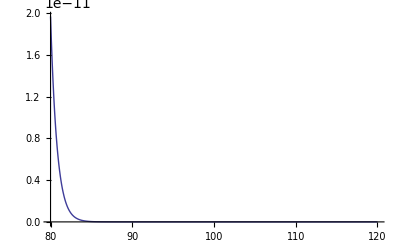

```mathematica
Plot[(1+Erf[(100-x-x)/(√(2x))]),{x,80,120},PlotRange->All]
```

```mathematica
?Series
```

Series[f,{x,x_0,n}] generates a power series expansion for f about the point x=x_0 to order (x-x_0)^n. 
Series[f,{x,x_0,n_x},{y,y_0,n_y}] successively finds series expansions with respect to x, then y.

```mathematica
Series[Erf[x],{x,∞,1}]
```

1+ⅇ^(-x^2) (-1/(√π x)+O[1/x]^2)

```mathematica
Series[Erf[x],{x,-∞,1}]
```

-1+ⅇ^(-x^2) (-1/(√π x)+O[1/x]^2)

P(A∧¬B)=1/2 ⅇ^(-λ(T-μ-λ σ^2/2))(erf((μ+λ σ^2)/(√2 σ))+erf((T-μ-λ σ^2)/(√2 σ)))

Approximation for large negative T-μ-λ σ^2.

P(A∧¬B)=1/2 ⅇ^(-λ(T-μ-λ σ^2/2))(1-1/(√π((μ+λ σ^2)/(√2 σ)))exp(-((μ+λ σ^2)/(√2 σ))^2)-1-1/(√π((T-μ-λ σ^2)/(√2 σ)))exp(-((T-μ-λ σ^2)/(√2 σ))^2))

P(A∧¬B)=1/2 ⅇ^(-λ(T-μ-λ σ^2/2))(-1/(√π((μ+λ σ^2)/(√2 σ)))exp(-((μ+λ σ^2)/(√2 σ))^2)-1/(√π((T-μ-λ σ^2)/(√2 σ)))exp(-((T-μ-λ σ^2)/(√2 σ))^2))

```mathematica
1/2 ⅇ^(-λ(T-μ-λ σ^2/2))(-1/(√π((μ+λ σ^2)/(√2 σ)))Exp[-((μ+λ σ^2)/(√2 σ))^2]-1/(√π((T-μ-λ σ^2)/(√2 σ)))Exp[-((T-μ-λ σ^2)/(√2 σ))^2])//FullSimplify
```

(ⅇ^(1/2 λ (-2 T+2 μ+λ σ^2)) σ (-(ⅇ^(-((-T+μ+λ σ^2)^2)/(2 σ^2)))/(T-μ-λ σ^2)-(ⅇ^(-((μ+λ σ^2)^2)/(2 σ^2)))/(μ+λ σ^2)))/(√(2 π))

```mathematica
1/2 ⅇ^(-λ(T-μ-λ σ^2/2))(-1/(√π((T-μ-λ σ^2)/(√2 σ)))Exp[-((T-μ-λ σ^2)/(√2 σ))^2])//Simplify
```

(ⅇ^(-(T-μ)^2/(2 σ^2)) σ)/(√(2 π) (-T+μ+λ σ^2))

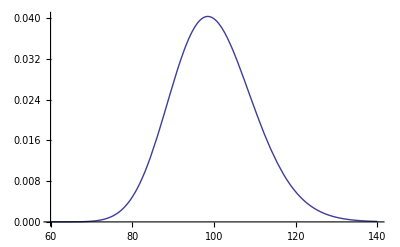

```mathematica
Plot[(√x)/(√(2π)(x+x-100))Exp[-(100-x)^2/(2x)],{x,60,140},PlotRange->All]
```

```mathematica
NIntegrate[(√x)/(√(2π)(x+x-100))Exp[-(100-x)^2/(2x)],{x,60,140}]
```

1.01034